```mathematica
<<Neurogrid`
```

Notation::difform: The defined current default input format TraditionalForm`StandardForm differs from the current default output format TraditionalForm`TraditionalForm. The WorkingForm option will default to the current default output format, but the Notations, Symbolizations, and InfixNotations may behave differently than expected.

## ADC mismatch analysis

```mathematica
ImageResize[Import["/home/noza/work/Schematic Pictures/1V_ADC.png"],600]
```

-Graphics-

### Background

This section will analyze the 1V ADC design that is an adaptation of the New Gray Code ADC that is described on the wiki.  The goal of this analysis is to find I_Rout in terms of mismatch applied to I_Rin, and I_Sout in terms of mismatch applied to I_Sin.The operation of this ADC should be the same as the design on the wiki, except that it has been modified for 1V operation.  This means that the following equations describe the general operation of the ADC, where D_out is the digital bit that is output for the ADC stage in question, and I_Sout and I_Rout are the Signal and Reference currents, respectively, that are output to the next stage of the ADC.

D_out=I_Sin>I_Rin
I_Sout=2*Min(I_Sin,I_Rin)
I_Rout=Abs(I_Rin-I_Sin)

For the purposes of clarity, I have changed the naming convention from the wiki.  What used to be I_inV is now I_Sin, where the S stands for Signal.  In other words, this is trying to clarify that the signal that we are trying to digitize is I_Sin.  In order to digitize it is compared to I_Rin, where the R stands for Reference.  This signal is the same as I_inV on the wiki.  These naming conventions also apply to the output currents.

Transistors M_S_ and M_R_ comprise the portion of the ADC that determine I_Sout.  Likewise, transistors M_D_ calculate the absolute value of the Difference between I_Rin and I_Sin which gets sent on to the next stage as I_Rout.

Based on Ben's DAC Mismatch analysis and his characterization of transistor mismatch, we assume that the transistor threshold difference, normalized by U_T, can be assume to come from a log-normal distribution, defined by LogNormal[0, σ].

I assume that I_Sin and I_Rin are the reference currents from which mismatch will be compared.  This means that we don't need to include a mismatch term for I_Sin or I_Rin.

For this mismatch analysis, I have denoted the four branch currents, I_1, I_2, I_3, and I_4, individually.  This will hopefully make analyzing the mismatch easier, as each current will have a different mismatch constant taken from a distribution.  The mismatch constants will be written as as either s__ or r__ (depending on whether the mismatch is with relation to I_Sin or I_Rin, respectively, where _ is the unique identifier of the transistor that differs.   For instance, OverBar[I_Sin]=s_B2 I_Sin, where if s_B2 was equal to 1 (if M_B2 was exactly like M_B1), then OverBar[I_Sin]== I_Sin

To begin with, we know, based on circuit current analysis,  that:

OverBar[I_Sin]=s_B2 I_Sin
OverBar[I_Sin]=I_1+I_DS
I_Rin=I_4+I_DR
I_Sout=I_2+I_3
I_Rout=I_DS+I_DR
I_Rout≃|OverBar[I_Sin]-I_Rin|

Of these basic equations, the sixth (I_Rout) is the only one where the derivation/result is a little unintuitive.  As such, the analysis is written below:

I_Rout=OverBar[I_Sin]-I_1+I_Rin-I_4

Because of the nature of the upper portion of the circuit (the Min function calculator), we can assume that I_1≃I_4.  More importantly, the value of each of those currents will roughly equal Min(OverBar[I_Sin], I_Rin).  Therefore, I_Rout can equal either of the following equations, which is the same as the absolute value of the difference between I_Sin and I_Rin

I_Rout≃OverBar[I_Sin]-OverBar[I_Sin]+I_Rin-OverBar[I_Sin]=I_Rin-OverBar[I_Sin]
I_Rout≃OverBar[I_Sin]-I_Rin+I_Rin-I_Rin=OverBar[I_Sin]-I_Rin

### Mismatch in I_Sout

The first thing to note when analyzing the ADC circuit, is that there are 4 possible, high-level input situations depending on the following conditions:

I_Sin>>I_Rin	I_Sin is much greater than I_Rin
I_Sin≳I_Rin	I_Sin is only barely greater than I_Rin
I_Sin≲I_Rin	I_Sin is only barely smaller than I_Rin
I_Sin<<I_Rin	I_Sin is much smaller than I_Rin

In the first and last situations, the analysis is much easier than in the 2^nd or 3^rd situations.  This results from the fact that when the values of I_Sin≃I_Rin, then the mismatch can cause the circuit to activate I_S1 and I_R2 simultaneously.  This is a confounding factor because if there was no mismatch, then we could assume that if I_S1 is active, then so are I_S2,I_S3,and I_S4.  This would also apply to the I_R_ currents if they were active.

In the first case (I_Sin>>I_Rin), the following equations would apply:

I_1=r_R1/r_R4 I_Rin
I_2=r_R2/r_R4 I_Rin
I_3=r_R3/r_R4 I_Rin
I_4=I_Rin

I_Sout=(r_R2+r_R3)I_Rin/r_R4

In the last case (I_Sin<<I_Rin), the following equations would apply:

I_1=s_B2/s_B1 I_Sin
I_2=(s_S2 s_B2)/(s_S1 s_B1)I_Sin
I_3=(s_S3 s_B2)/(s_S1 s_B1)I_Sin
I_4=(s_S4 s_B2)/(s_S1 s_B1)I_Sin

I_Sout=(s_S2+s_S3)(s_B2 I_Sin)/(s_S1 s_B1)

In the 2^nd and 3^rd cases (I_Sin≳I_Rin, I_Sin≲I_Rin), the following equations would apply.  It should be noted that we are handling the 2^nd and 3^rd cases as the same situation because these situations are the same as saying when I_Sin≃I_Rin, where roughly equals is defined as within the mismatch’s effect to cause a transistor to turn on when it’s native value deems that it should turn off.

I_1=Min(r_R1/r_R4 I_Rin,s_B2/s_B1 I_Sin)
I_2=Min(r_R2/r_R4 I_Rin,(s_S2 s_B2)/(s_S1 s_B1)I_Sin)
I_3=Min(r_R3/r_R4 I_Rin,(s_S3 s_B2)/(s_S1 s_B1)I_Sin)
I_4=Min(I_Rin,(s_S4 s_B2)/(s_S1 s_B1)I_Sin)

I_Sout=Min(r_R2/r_R4 I_Rin,(s_S2 s_B2)/(s_S1 s_B1)I_Sin)+Min(r_R3/r_R4 I_Rin,(s_S3 s_B2)/(s_S1 s_B1)I_Sin)

It should be noted that this final result is actually the most general form of the mismatch of I_Sout because it also applies to the first two cases.  As such, moving forward, I will be using the 4 equations for each path’s current mismatch in my analysis.

### Revised mismatch in I_Sout

```mathematica
FullSimplify[Solve[{
Subscript[Ι, 1]==s1(Subscript[Ι, s1f]-Subscript[Ι, s1r]),
Subscript[Ι, 1]==r1(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 2]==s2(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]),
Subscript[Ι, 3]==s3(Subscript[Ι, s3f]),
Subscript[Ι, 3]==r3(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
Subscript[Ι, 4]==s4(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 4]==r4(Subscript[Ι, r4f]-Subscript[Ι, r4r]),

Subscript[Ι, s1f]==Subscript[Ι, s2f],
Subscript[Ι, r4f]==Subscript[Ι, r3f],

Subscript[Ι, s1r] Subscript[Ι, r2f]==Subscript[Ι, r1f] Subscript[Ι, s2r],
Subscript[Ι, s1r] Subscript[Ι, r3r]==Subscript[Ι, r1f] Subscript[Ι, s3f],
Subscript[Ι, s1r] Subscript[Ι, r4r]==Subscript[Ι, r1f] Subscript[Ι, s4f],
Subscript[Ι, s2r] Subscript[Ι, r3r]==Subscript[Ι, r2f] Subscript[Ι, s3f],
Subscript[Ι, s2r] Subscript[Ι, r4r]==Subscript[Ι, r2f] Subscript[Ι, s4f],
Subscript[Ι, r3r] Subscript[Ι, s4f]==Subscript[Ι, s3f] Subscript[Ι, r4r]
},{(*Subscript[Ι, Sout],*)Subscript[Ι, s1f],Subscript[Ι, s1r],Subscript[Ι, r1f],Subscript[Ι, r1r],Subscript[Ι, s2f],Subscript[Ι, s2r],Subscript[Ι, r2f],(*Subscript[Ι, r2r],*)Subscript[Ι, s3f],(*Subscript[Ι, s3r],*)Subscript[Ι, r3f],Subscript[Ι, r3r],Subscript[Ι, s4f],Subscript[Ι, s4r],Subscript[Ι, r4f],Subscript[Ι, r4r],Subscript[Ι, 2],Subscript[Ι, 3]}],Subscript[Ι, 1]>0&&Subscript[Ι, 2]>0&&Subscript[Ι, 3]>0&&Subscript[Ι, 4]>0&&s1>0&&r1>0&&s2>0&&r2>0&&s3>0&&r3>0&&s4>0&&r4>0]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→(s2 Ι_s1r (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1 Ι_s2r),Ι_r1r→(-(r2 Ι_1)/r1-s2 Ι_s1r+(s2 Ι_s1r (Ι_1+s1 Ι_s1r))/(s1 Ι_s2r))/r2,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_r2f→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1),Ι_r3f→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r),Ι_r3r→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)) Ι_s3f)/(r2 s1 Ι_s2r),Ι_s4f→(r4 (r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 Ι_4 Ι_s2r)/(r3 r4 s2 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_s4r→(r4 s4 (r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r3 Ι_4 (r4 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s4-r4 s2) Ι_s2r))/(r3 r4 s2 s4 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_r4f→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r),Ι_r4r→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r)-Ι_4/r4,Ι_2→s2 (Ι_1/s1+Ι_s1r-Ι_s2r),Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_r2f→(s2 (Ι_1-s1 Ι_s2r))/(r2 s1),Ι_r3f→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f,Ι_r3r→(s2 (Ι_1-s1 Ι_s2r) Ι_s3f)/(r2 s1 Ι_s2r),Ι_s4f→(r4 (r3 s2 Ι_1+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 Ι_4 Ι_s2r)/(r3 r4 s2 (Ι_1-s1 Ι_s2r)),Ι_s4r→(r3 r4 s2 Ι_1 (s4 Ι_s3f-Ι_4)+s1 Ι_s2r (r3 (r4 s2-r2 s4) Ι_4+r4 (r2 s3-r3 s2) s4 Ι_s3f))/(r3 r4 s2 s4 (Ι_1-s1 Ι_s2r)),Ι_r4f→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f,Ι_r4r→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f-Ι_4/r4,Ι_2→(s2 Ι_1)/s1-s2 Ι_s2r,Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1r→Ι_r1f-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_s2r→0,Ι_r2f→(s2 Ι_1)/(r2 s1),Ι_s3f→0,Ι_r3f→Ι_r3r,Ι_s4f→0,Ι_s4r→-Ι_4/s4,Ι_r4f→Ι_r3r,Ι_r4r→Ι_r3r-Ι_4/r4,Ι_2→(s2 Ι_1)/s1,Ι_3→0},{Ι_s1f→0,Ι_s1r→-Ι_1/s1,Ι_r1r→Ι_r1f-Ι_1/r1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_r3f→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f,Ι_r3r→-(s1 Ι_r1f Ι_s3f)/Ι_1,Ι_s4f→(r3 Ι_1 Ι_4+r4 (r3 s1 Ι_r1f-s3 Ι_1) Ι_s3f)/(r3 r4 s1 Ι_r1f),Ι_s4r→Ι_4 (Ι_1/(r4 s1 Ι_r1f)-1/s4)+(1-(s3 Ι_1)/(r3 s1 Ι_r1f)) Ι_s3f,Ι_r4f→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f,Ι_r4r→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f-Ι_4/r4,Ι_2→0,Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_s2r→Ι_1/s1+Ι_s1r,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4},{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→(s2 Ι_s1r (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1 Ι_s2r),Ι_r1r→(-(r2 Ι_1)/r1-s2 Ι_s1r+(s2 Ι_s1r (Ι_1+s1 Ι_s1r))/(s1 Ι_s2r))/r2,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_r2f→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1),Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 Ι_4 Ι_s2r)/(r4 s2 Ι_1+r4 s1 s2 Ι_s1r-r4 s1 s2 Ι_s2r),Ι_s4r→(Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2 (Ι_1+s1 Ι_s1r)))/(r4 s2 s4 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_r4f→0,Ι_r4r→-Ι_4/r4,Ι_2→s2 (Ι_1/s1+Ι_s1r-Ι_s2r),Ι_3→0},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_s2r→Ι_1/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_r2f→(s2 (Ι_1-s1 Ι_s2r))/(r2 s1),Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 Ι_4 Ι_s2r)/(r4 s2 Ι_1-r4 s1 s2 Ι_s2r),Ι_s4r→-(Ι_4 (r4 s2 Ι_1+s1 (r2 s4-r4 s2) Ι_s2r))/(r4 s2 s4 (Ι_1-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4/r4,Ι_2→(s2 Ι_1)/s1-s2 Ι_s2r,Ι_3→0},{Ι_s1f→0,Ι_s1r→-Ι_1/s1,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4}}

```mathematica
FullSimplify[Solve[{
(*Subscript[Ι, 4]==r4(Subscript[Ι, r4f]-Subscript[Ι, r4r]),
Subscript[Ι, 4]==s4(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 3]==r3(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
(*Subscript[Ι, 3]==s3(Subscript[Ι, s3f]-Subscript[Ι, s3r]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]-Subscript[Ι, r2r]),*)
Subscript[Ι, 3]==s3(Subscript[Ι, s3f]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]),
Subscript[Ι, 2]==s2(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 1]==r1(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 1]==s1(Subscript[Ι, s1f]-Subscript[Ι, s1r]),*)
Subscript[Ι, 1]==(Subscript[Ι, s1f]-Subscript[Ι, s1r]),
Subscript[Ι, 1]==(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 2]==(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 2]==(Subscript[Ι, r2f]),
(*Subscript[Ι, 2]==(Subscript[Ι, r2f]-Subscript[Ι, r2r]),
Subscript[Ι, 3]==(Subscript[Ι, s3f]-Subscript[Ι, s3r]),*)
Subscript[Ι, 3]==(Subscript[Ι, s3f]),
Subscript[Ι, 3]==(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
Subscript[Ι, 4]==(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 4]==(Subscript[Ι, r4f]-Subscript[Ι, r4r]),

(*Subscript[Ι, Sout]==Subscript[Ι, 2]+Subscript[Ι, 3],*)
Subscript[Ι, s1f]/s1==Subscript[Ι, s2f]/s2,
Subscript[Ι, r4f]/r4==Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s2r]/s2==Subscript[Ι, s1r]/s1 Subscript[Ι, r2f]/r2 Subscript[Ι, s2f]/s2,
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r3r]/r3==Subscript[Ι, r4r]/r4 Subscript[Ι, s3f]/s3 Subscript[Ι, r3f]/r3,*)
Subscript[Ι, s1r]/s1 Subscript[Ι, r2f]/r2==Subscript[Ι, r1f]/r1 Subscript[Ι, s2r]/s2,
Subscript[Ι, s1r]/s1 Subscript[Ι, r3r]/r3==Subscript[Ι, r1f]/r1 Subscript[Ι, s3f]/s3,
Subscript[Ι, s1r]/s1 Subscript[Ι, r4r]/r4==Subscript[Ι, r1f]/r1 Subscript[Ι, s4f]/s4,
Subscript[Ι, s2r]/s2 Subscript[Ι, r3r]/r3==Subscript[Ι, r2f]/r2 Subscript[Ι, s3f]/s3,
Subscript[Ι, s2r]/s2 Subscript[Ι, r4r]/r4==Subscript[Ι, r2f]/r2 Subscript[Ι, s4f]/s4,
Subscript[Ι, r3r]/r3 Subscript[Ι, s4f]/s4==Subscript[Ι, s3f]/s3 Subscript[Ι, r4r]/r4

(*Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s3r]/s3 Subscript[Ι, r3r]/r3==Subscript[Ι, s2r]/s2 Subscript[Ι, r2r]/r2 Subscript[Ι, s3f]/s3 Subscript[Ι, r3f]/r3,
Subscript[Ι, r3r]/r3 Subscript[Ι, s3r]/s3==Subscript[Ι, s3f]/s3 Subscript[Ι, r2r]/r2,
Subscript[Ι, s2r]/s2 Subscript[Ι, r2r]/r2==Subscript[Ι, r2f]/r2 Subscript[Ι, s3r]/s3,*)

(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1==Subscript[Ι, s1r]/s1 Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1==Subscript[Ι, s1r]/s1 Subscript[Ι, r4f]/r4,*)
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2==Subscript[Ι, s2r]/s2 Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2==Subscript[Ι, s2r]/s2 Subscript[Ι, r4f]/r4,*)
(*Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3==Subscript[Ι, r3r]/r3 Subscript[Ι, s1f]/s1,*)
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3==Subscript[Ι, r3r]/r3 Subscript[Ι, s2f]/s2,
(*Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4==Subscript[Ι, r4r]/r4 Subscript[Ι, s1f]/s1,*)
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4==Subscript[Ι, r4r]/r4 Subscript[Ι, s2f]/s2,
Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s3f]/s3==Subscript[Ι, s1r]/s1 Subscript[Ι, r3r]/r3 Subscript[Ι, s2f]/s2,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s4f]/s4==Subscript[Ι, s1r]/s1 Subscript[Ι, r4r]/r4 Subscript[Ι, s2f]/s2,
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s3f]/s3==Subscript[Ι, s2r]/s2 Subscript[Ι, r3r]/r3 Subscript[Ι, s1f]/s1,
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s4f]/s4==Subscript[Ι, s2r]/s2 Subscript[Ι, r4r]/r4 Subscript[Ι, s1f]/s1,
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3 Subscript[Ι, r1f]/r1==Subscript[Ι, r3r]/r3 Subscript[Ι, s1r]/s1 Subscript[Ι, r4f]/r4,
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3 Subscript[Ι, r2f]/r2==Subscript[Ι, r3r]/r3 Subscript[Ι, s2r]/s2 Subscript[Ι, r4f]/r4,
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r1f]/r1==Subscript[Ι, r4r]/r4 Subscript[Ι, s1r]/s1 Subscript[Ι, r3f]/r3,*)
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r2f]/r2==Subscript[Ι, r4r]/r4 Subscript[Ι, s2r]/s2 Subscript[Ι, r3f]/r3*)
},{Subscript[Ι, 2],Subscript[Ι, 3],(*Subscript[Ι, Sout],*)Subscript[Ι, s1f],Subscript[Ι, s1r],Subscript[Ι, r1f],Subscript[Ι, r1r],Subscript[Ι, s2f],Subscript[Ι, s2r],Subscript[Ι, r2f],(*Subscript[Ι, r2r],*)Subscript[Ι, s3f],(*Subscript[Ι, s3r],*)Subscript[Ι, r3f],Subscript[Ι, r3r],Subscript[Ι, s4f],Subscript[Ι, s4r],Subscript[Ι, r4f],Subscript[Ι, r4r]}],Subscript[Ι, 1]>0&&Subscript[Ι, 2]>0&&Subscript[Ι, 3]>0&&Subscript[Ι, 4]>0&&s1>0&&r1>0&&s2>0&&r2>0&&s3>0&&r3>0&&s4>0&&r4>0]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Ι_2→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_3→Ι_s3f,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→(r1 s2 Ι_s1r (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r))/(r2 s1^2 Ι_s2r),Ι_r1r→(r1 s2^2 Ι_s1r (Ι_1+Ι_s1r)-s1 (r2 s1 Ι_1+r1 s2 Ι_s1r) Ι_s2r)/(r2 s1^2 Ι_s2r),Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_r3f→((r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_r3r→(r3 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_s4f→(r4 s4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 s3 s4 Ι_4 Ι_s2r)/(r3 r4 s2 s3 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_s4r→(r3 s3 Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2^2 (Ι_1+Ι_s1r))+r4 s4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r3 r4 s2 s3 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_r4f→(r4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r),Ι_r4r→(r4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r)-Ι_4},{Ι_2→(s2 Ι_1)/s1-Ι_s2r,Ι_3→Ι_s3f,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_r2f→(s2 Ι_1)/s1-Ι_s2r,Ι_r3f→((r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_r3r→(r3 s2 (s2 Ι_1-s1 Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_s4f→(s4 (r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 s3 Ι_4 Ι_s2r))/(r3 r4 s2 s3 (s2 Ι_1-s1 Ι_s2r)),Ι_s4r→(r3 r4 Ι_1 (s4 Ι_s3f-s3 Ι_4) s2^2+s1 Ι_s2r (r3 s3 (r4 s2-r2 s4) Ι_4+r4 (r2 s3-r3 s2) s4 Ι_s3f))/(r3 r4 s2 s3 (s2 Ι_1-s1 Ι_s2r)),Ι_r4f→(r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r),Ι_r4r→(r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r)-Ι_4},{Ι_2→(s2 Ι_1)/s1,Ι_3→0,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1r→Ι_r1f-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_s2r→0,Ι_r2f→(s2 Ι_1)/s1,Ι_s3f→0,Ι_r3f→Ι_r3r,Ι_s4f→0,Ι_s4r→-Ι_4,Ι_r4f→(r4 Ι_r3r)/r3,Ι_r4r→(r4 Ι_r3r)/r3-Ι_4},{Ι_2→0,Ι_3→Ι_s3f,Ι_s1f→0,Ι_s1r→-Ι_1,Ι_r1r→Ι_r1f-Ι_1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_r3f→(1-(r3 s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f,Ι_r3r→-(r3 s1 Ι_r1f Ι_s3f)/(r1 s3 Ι_1),Ι_s4f→(s4 (r3 r4 s1 Ι_r1f Ι_s3f+r1 s3 Ι_1 (r3 Ι_4-r4 Ι_s3f)))/(r3 r4 s1 s3 Ι_r1f),Ι_s4r→(r1 s3 s4 Ι_1 (r3 Ι_4-r4 Ι_s3f)+r3 r4 s1 Ι_r1f (s4 Ι_s3f-s3 Ι_4))/(r3 r4 s1 s3 Ι_r1f),Ι_r4f→r4 (1/r3-(s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f,Ι_r4r→r4 (1/r3-(s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_s2r→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0},{Ι_2→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_3→0,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→(r1 s2 Ι_s1r (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r))/(r2 s1^2 Ι_s2r),Ι_r1r→(r1 s2^2 Ι_s1r (Ι_1+Ι_s1r)-s1 (r2 s1 Ι_1+r1 s2 Ι_s1r) Ι_s2r)/(r2 s1^2 Ι_s2r),Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 s4 Ι_4 Ι_s2r)/(r4 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_s4r→(Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2^2 (Ι_1+Ι_s1r)))/(r4 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_s2r→(s2 Ι_1)/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0},{Ι_2→(s2 Ι_1)/s1-Ι_s2r,Ι_3→0,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_r2f→(s2 Ι_1)/s1-Ι_s2r,Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 s4 Ι_4 Ι_s2r)/(r4 s2^2 Ι_1-r4 s1 s2 Ι_s2r),Ι_s4r→-(Ι_4 (r4 Ι_1 s2^2+s1 (r2 s4-r4 s2) Ι_s2r))/(r4 s2 (s2 Ι_1-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→0,Ι_s1r→-Ι_1,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0}}

### Mismatch in I_Rout

To analyze the mismatch in I_Rout, we start at the equation that most generally defines I_Rout.  From there, we use our I_Sout analysis to apply the mismatch that I_1 and I_4 would introduce to the circuit.

I_Rout=OverBar[I_Sin]-I_1+I_Rin-I_4
I_Rout=s_B2/s_B1 I_Sin-I_1+I_Rin-I_4

I_Rout=s_B2/s_B1 I_Sin-Min(r_R1/r_R4 I_Rin,s_B2/s_B1 I_Sin)+I_Rin-Min(I_Rin,(s_S4 s_B2)/(s_S1 s_B1)I_Sin)

### Function definitions for I_Sout and I_Rout

```mathematica
ISout[ISin_,IRin_,sB1_, sB2_,sS1_, rR2_,sS2_,rR3_,sS3_,rR4_]:=FullSimplify[Min[rR2/rR4 IRin, (sS2 sB2)/(sS1 sB1)ISin]+Min[rR3/rR4 IRin,(sS3 sB2)/(sS1 sB1)ISin],{IRin≥0,ISin≥0,sB1>0,sB2>0,sS1>0,rR2>0,sS2>0,rR3>0,sS3>0,rR4>0}]
IRout[ISin_,IRin_,sB1_,sB2_ ,rR1_,sS1_,rR4_,sS4_]:=FullSimplify[sB2/sB1 ISin-Min[rR1/rR4 IRin, sB2/sB1 ISin]+IRin-Min[IRin,(sS4 sB2)/(sS1 sB2) ISin],{IRin≥0,ISin≥0,sB1>0,sB2>0,rR1>0,sS1>0,rR4>0,sS4>0}]
ISoutList[ISins_,IRins_,sB1_, sB2_,sS1_, rR2_,sS2_,rR3_,sS3_,rR4_]:=FullSimplify[Min/@Transpose[{rR2/rR4 IRins, (sS2 sB2)/(sS1 sB1)ISins}]+Min/@Transpose[{rR3/rR4 IRins,(sS3 sB2)/(sS1 sB1)ISins}],{IRins≥0,ISins≥0,sB1>0,sB2>0,sS1>0,rR2>0,sS2>0,rR3>0,sS3>0,rR4>0}]
IRoutList[ISins_,IRins_,sB1_,sB2_ ,rR1_,sS1_,rR4_,sS4_]:=FullSimplify[sB2/sB1 ISins-Min/@Transpose[{rR1/rR4 IRins, sB2/sB1 ISins}]+IRins-Min/@Transpose[{IRins,(sS4 sB2)/(sS1 sB2) ISins}],{IRins≥0,ISins≥0,sB1>0,sB2>0,rR1>0,sS1>0,rR4>0,sS4>0}]
```

```mathematica
"I_Sout"==ISout["I_Sin","I_Rin","s_B1","s_B2","s_S1","r_R2","s_S2","r_R3","s_S3","r_R4"]
"I_Rout"==IRout["I_Sin","I_Rin","s_B1","s_B2","r_R1","s_s1","r_R4","s_S4"]
```

I_Sout==min((I_Rin r_R2)/r_R4,(I_Sin s_B2 s_S2)/(s_B1 s_S1))+min((I_Rin r_R3)/r_R4,(I_Sin s_B2 s_S3)/(s_B1 s_S1))

I_Rout==-min((I_Rin r_R1)/r_R4,(I_Sin s_B2)/s_B1)-min(I_Rin,(I_Sin s_S4)/s_s1)+I_Rin+(I_Sin s_B2)/s_B1

### Function definition for D_out

D_out is the digital output bit that returns True if I_Sin>I_Rin and False if otherwise.  It returns the True/False as 1/0 (respectively), so that eventually I can easily see the boolean value of the output code.

```mathematica
Dout[ISin_, IRin_]:=Boole[Positive[ISin-IRin]]
Dout[ISin_, IRin_,ISin0_,IRin0_]:=If[ISin==IRin,If[ISin0>IRin0,1,0],Boole[ISin>IRin]]
```

### Function definitions for distributions

From Ben’s device analysis, we know that the mismatch parameter comes from a log-normal distribution.  The log-normal distribution comes from a normal distribution.  In other words, if X comes from a normal distribution (X∼𝒩(μ_n,σ_n^2)), then Y is defined as a log-normal distribution according to the following equation, Y=ⅇ^X.  The log-normal statistics (σ_l & μ_l) are related to normal’s  (σ_n & μ_n) according to the following two equations:

```mathematica
μLogNormal[μn_,σn_]=Mean[LogNormalDistribution[μn,σn]];
σLogNormal[μn_,σn_]=Simplify[Exp[Log[PowerExpand[StandardDeviation[LogNormalDistribution[μn,σn]]]]]];
Subscript[μ, l]-> μLogNormal[Subscript[μ, n],Subscript[σ, n]]
Subscript[σ, l]-> σLogNormal[Subscript[μ, n],Subscript[σ, n]]
```

μ_l→ⅇ^(μ_n+σ_n^2/2)

σ_l→√(ⅇ^(σ_n^2)-1) ⅇ^(μ_n+σ_n^2/2)

When σ_n^2≪1, these simplify to

```mathematica
μLogNormalApprox[μn_]=Simplify[PowerExpand[μLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
σLogNormalApprox[μn_,σn_]=Simplify[PowerExpand[σLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
Subscript[μ, l]-> μLogNormalApprox[Subscript[μ, n]]
Subscript[σ, l]-> σLogNormalApprox[Subscript[μ, n],Subscript[σ, n]]
```

μ_l→ⅇ^μ_n

σ_l→ⅇ^μ_n √(ⅇ^(σ_n^2)-1)

Assume we only have access to a log-normal distribution Y, defined as Y~ln𝒩(μ_n,σ_n^2), but we don’t know the underlying normal distribution’s statistics (μ_n, σ_n).  We can get the mean and standard deviation of the distribution (μ_l, σ_l) and then calculate/approximate the underlying normal’s mean and standard deviation based on the following two equations:

```mathematica
σNormal[μl_,σl_]=Refine[Reduce[σl^2==(σLogNormal[μn,σn]/.ⅇ^(μn+σn^2/2) -> μl)^2,σn],C[1]==0&&μl>0&&σl>0&&σn>0]⟦2,2⟧;
μNormal[μl_,σl_]=Refine[Reduce[μl==μLogNormal[μn,σNormal[μl,σl]]&&μl>0,μn],C[1]==0&&μl>0&&σl>0]⟦2⟧;
Subscript[μ, n]-> μNormal[Subscript[μ, l],Subscript[σ, l]]
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
```

μ_n→log(Root[#1^4 (μ_l^2+σ_l^2)-#1^2 μ_l^4&,4])

σ_n→√(log((μ_l^2+σ_l^2)/μ_l^2))

Similar to the LogNormal analysis above, for σ_l^2≪1, the equation for μ_n simplifes as written below.  For σ_n, we don’t simplify it based on this assumption, because if we did σ_n would always equal 0, which is obviously incorrect.

```mathematica
μNormalApprox[μl_]=μn/.Refine[Solve[μl==μLogNormalApprox[μn],μn],C[1]==0]⟦1,1⟧;
Subscript[μ, n]-> μNormalApprox[Subscript[μ, l]]
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
```

μ_n→log(μ_l)

σ_n→√(log((μ_l^2+σ_l^2)/μ_l^2))

### Plot of distribution of mismatch parameters

The following plot shows the log-normal distribution from which the mismatch terms are taken (in blue) and the normal distribution, 𝒩(μ_l,σ_l), that approximates this log-normal distribution (in orange).

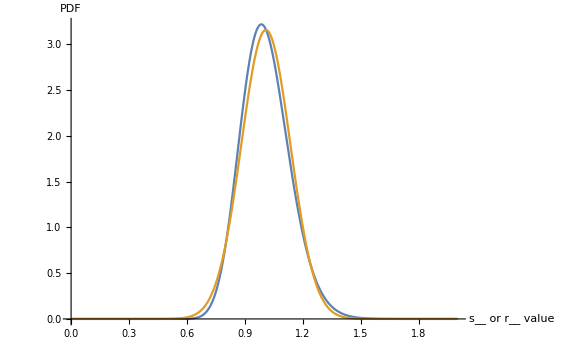

```mathematica
With[{μn=0, σn=0.125},
Plot[{
PDF[LogNormalDistribution[μn,σn],x],
PDF[NormalDistribution[μLogNormal[μn,σn],σLogNormal[μn,σn]],x]
},
{x,0,2},PlotRange->All,ImageSize->Large,AxesLabel->{"s__ or r__ value", "PDF"}]
]
```

```mathematica
PDFLNormDist[x_,μn_,σn_]:=PDF[LogNormalDistribution[μn,σn],x]
```

The following calculation shows that the probability of getting a negative number from the mismatch parameters is nearly 0, if we assume that the distribution is LogNormal[μ_n=0,σ_n=0.125].

```mathematica
PDFLNormDist[#,0,0.125]&/@{-0.01,-0.001,-0.0001,-0.00001,-0.000001,0,0.000001}
```

{0,0,0,0,0,0,8.43282181235552×10^-2647}

### Theoretical and numerical analysis of 1 ADC stage

```mathematica
Manipulate[
With[{μn=0,σn=0.125,numSamples=10^5,numBins=100},
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData=Select[RandomVariate[distISout,numSamples],#>0&];
distISoutEst=EstimatedDistribution[distISoutData,LogNormalDistribution[μs,σs]];
distISoutHist=HistogramDistribution[distISoutData,numBins];
(*
I'm throwing away data points that were selected that result in IRout to equal 0.  I do this because in practice, one of the two currents will always be somewhat larger than the other, therefore, there should always be some current going out Subscript[I, Rout]
*)
distIRoutData=Select[ RandomVariate[distIRout,numSamples],#>0&];
distIRoutEst=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
pISout=PDF[distISoutHist,x];
pIRout=PDF[distIRoutHist,x];
Grid[{{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}]
},(*{
Grid[{
{Style["I_Sout Estimated Distribution:"],distISoutEst},
{Style["I_Rout Estimated Distribution:"],distIRoutEst}
}]
},*){
Show[
DiscretePlot[{pISout,pIRout},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->Large,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst,x],PDF[distIRoutEst,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Large]
]
}}]
],
{{ISin,0.333333,"I_Sin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{IRin,0.666666,"I_Rin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{xMin,0,"x_min"},-0.5,0.5,0.1,Appearance->{"Labeled","Open"}},
{{xMax,2.0,"x_max"},0.5,5,0.1,Appearance->{"Labeled","Open"}}
]
```

### Theoretical and numerical analysis of 2 ADC stages

```mathematica
Manipulate[
With[{μn=0,σn=0.125/√2,numSamples=10^5,numBins=100,imgSz=500},
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData=Select[RandomVariate[distISout,numSamples],#>0&];
distISoutEst=EstimatedDistribution[distISoutData,LogNormalDistribution[μs,σs]];
distISoutHist=HistogramDistribution[distISoutData,numBins];
distIRoutData=Select[RandomVariate[distIRout,numSamples],#>0&];
distIRoutEst=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
pISout=PDF[distISoutHist,x];
pIRout=PDF[distIRoutHist,x];

distISout2= TransformedDistribution[ISout[ISin2,IRin2,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{ISin2\[Distributed]distISoutEst,IRin2\[Distributed]distIRoutEst,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout2= TransformedDistribution[IRout[ISin2,IRin2,sB1,sB2,rR1,sS1,rR4,sS4],{ISin2\[Distributed]distISoutEst,IRin2\[Distributed]distIRoutEst,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData2= Select[Flatten[RandomVariate[distISout2,numSamples]],#>0&];
(*distISoutEst2= EstimatedDistribution[distISoutData2,LogNormalDistribution[μs,σs]];*)
distISoutEst2= EstimatedDistribution[distISoutData2,NormalDistribution[μs,σs]];
distISoutHist2=HistogramDistribution[distISoutData2,numBins];
distIRoutData2 = Select[Flatten[RandomVariate[distIRout2,numSamples]],#>0&];
distIRoutEst2 = EstimatedDistribution[distIRoutData2,NormalDistribution[μr,σr]];
distIRoutHist2=HistogramDistribution[distIRoutData2,numBins];
pISout2=PDF[distISoutHist2,x];
pIRout2=PDF[distIRoutHist2,x];

Grid[{
{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}],
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist2],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist2]},
{Style["μ_I_Rout:"],Mean[distIRoutHist2],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist2]}
}]
},{
Show[
DiscretePlot[{pISout,pIRout},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->imgSz,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst,x],PDF[distIRoutEst,x]},{x,xMin,xMax},PlotRange->All,ImageSize->imgSz]
],
Show[
DiscretePlot[{pISout2,pIRout2},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->imgSz,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst2,x],PDF[distIRoutEst2,x]},{x,xMin,xMax},PlotRange->All,ImageSize->imgSz]
]
}
}]
],
{{ISin,0.666666,"I_Sin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{IRin,0.333333,"I_Rin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{xMin,0,"x_min"},-0.5,0.5,0.1,Appearance->{"Labeled","Open"}},
{{xMax,1.5,"x_max"},0.5,5,0.1,Appearance->{"Labeled","Open"}}
]
```

### Theoretical and numerical analysis of B ADC stages

```mathematica
distIoutB[ISin0_,IRin0_,B_]:=
Module[{ISin=ISin0,IRin=IRin0,curDistIoutB},
With[{μn=0,σn=0.0125},
If[B>1,
curDistIoutB=distIoutB[ISin,IRin,B-1];
distISout= TransformedDistribution[ISout[ISinB,IRinB,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{ISinB\[Distributed]curDistIoutB⟦1⟧,IRinB\[Distributed]curDistIoutB⟦2⟧,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISinB,IRinB,sB1,sB2,rR1,sS1,rR4,sS4],{ISinB\[Distributed]curDistIoutB⟦1⟧,IRinB\[Distributed]curDistIoutB⟦2⟧,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
,
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
];
{distISout,distIRout}
]
]
```

```mathematica
SeedRandom[1234];
getIoutData[B0_,ISin0_,IRin0_]:=Module[{B=B0,ISin=ISin0,IRin=IRin0},
With[{numSamples=10^5,numBins=100},
(*With[{μn=0,σn=0.125,numSamples=10^5,numBins=100,ISin=0.666666,IRin=0.333333},*)
distIout= distIoutB[ISin,IRin,B];
distISout=distIout⟦1⟧;
distIRout=distIout⟦2⟧;

distISoutData=RandomVariate[distISout,numSamples];
distISoutHist=HistogramDistribution[distISoutData,numBins];
distISoutEstNorm=EstimatedDistribution[distISoutData,NormalDistribution[μs,σs]];
distISoutEstLN=EstimatedDistribution[Select[distISoutData,#>0&],LogNormalDistribution[μs,σs]];

distIRoutData=RandomVariate[distIRout,numSamples];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
distIRoutEstNorm=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutEstLN=EstimatedDistribution[Select[distIRoutData,#>0&],LogNormalDistribution[μr,σr]];
];
{distISoutHist,distIRoutHist,distISoutEstNorm,distIRoutEstNorm,distISoutData,distIRoutData, distISoutEstLN, distIRoutEstLN}
]
```

```mathematica
With[{numB=4},
ISin0=0.5-1/2^numB;
IRin0=0.5+1/2^numB;
IOutTable=Table[getIoutData[b,ISin0,IRin0],{b,1,numB}];
]
```

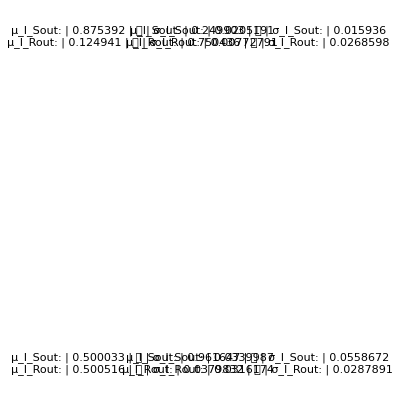
{I_Sin:,0.4375,	,I_Rin:,0.5625}
-Graphics-

```mathematica
With[{numB=4,xMin=0.0,xMax=1.5},
distPlots=Reap[
(
distISoutHist=IOutTable⟦#⟧⟦1⟧;
distIRoutHist=IOutTable⟦#⟧⟦2⟧;
distISoutEstNorm=IOutTable⟦#⟧⟦3⟧;
distIRoutEstNorm=IOutTable⟦#⟧⟦4⟧;
distISoutData=IOutTable⟦#⟧⟦5⟧;
distIRoutData=IOutTable⟦#⟧⟦6⟧;
distISoutEstLN=IOutTable⟦#⟧⟦7⟧;
distIRoutEstLN=IOutTable⟦#⟧⟦8⟧;

p1=DiscretePlot[{PDF[distISoutHist,x],PDF[distIRoutHist,x]},{x,xMin,xMax,0.01},ImageSize->Full,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue","PDF"}, PlotRange->All];
p2=Plot[{PDF[distISoutEstNorm,x],PDF[distIRoutEstNorm,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Full];
p3=Histogram[{distIRoutData,distIRoutData},50,"PDF"];
p4=Plot[{PDF[distISoutEstLN,x],PDF[distIRoutEstLN,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Full,PlotStyle->{Dashed,Dashed}];
Sow[
Grid[{
{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}]
},{
Show[{p1(*,p2,p4*)}]
}
}]]
)&/@Range[1,numB]];
Grid[{
{{Style["I_Sin:"],ISin0,"\t",Style["I_Rin:"],IRin0}},
{GraphicsGrid[ArrayReshape[distPlots⟦2⟧, {2, 2}], ImageSize->Full]}
}]
]
```

### Theoretical and numerical analysis of B ADC stages assuming 1 given ADC (as opposed to a population of ADCs)

The previous B-stage analysis assumed that at, essentially, we were analyzing numSamples worth of ADCs to see how their outputs would vary.  After my lab meeting talk about this, it was brought up that it would be wise to investigate just one ADC for all possible decoding values to see how many incorrect outputs the ADC would output.  This would help us better understand how many bits of depth we can go before any given ADC would have corrupt results.

This analysis will also use the new D_out function to try and output the actual binary code for each stage and input.

This following code sweeps over all 2^numB possible inputs, where numB is the number of bit resolution of the ADC (in other words, it’s the number of stages that the signal gets passed through).

#### Function to simulate an ideal/perfect ADC (one with no mismatch)

ADCSim0 is the function that calculates how an ideal ADC would perform for numB0 worth of stages

```mathematica
ADCSim0[numB0_]:=
Module[{numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
ISoutVal = ISout[ISin,IRin,1,1,1,1,1,1,1,1];
IRoutVal = IRout[ISin,IRin,1,1,1,1,1,1];
{ISoutVal,IRoutVal,Dout[Rationalize[ISoutVal],Rationalize[IRoutVal]]}
];
SweepISin[inputNum_]:=
Module[{num=inputNum},
ISin0=(2num-1)/2^(numB+1);
IRin0=1-ISin0;
out = NestList[distIout, {ISin0,IRin0, Dout[ISin0,IRin0]},numB-1];
List[
out,
Transpose[out]⟦3⟧
]
];
SweepISin[#]&/@Table[i,{i,2^numB}]
]
```

#### Function to simulate a mismatched ADC

ADCSim is a function that calculates how an ADC would operate if it had to output numB0 worth of stages

```mathematica
ADCSim[μn0_,σn0_,numB0_, seedNum_]:=
Module[{μn=μn0, σn=σn0, numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
ISoutVal = ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4];
rR1=RandomVariate[LNDist];
sS4=RandomVariate[LNDist];
IRoutVal = IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4];
{ISoutVal,IRoutVal,Dout[ISoutVal,IRoutVal]}
];
SweepISin[inputNum_]:=
Module[{num=inputNum},
SeedRandom[seedNum];
ISin0=(2num-1)/2^(numB+1);
IRin0=1-ISin0;
out = NestList[distIout, {ISin0,IRin0, Dout[ISin0,IRin0]},numB-1];
List[
out,
Transpose[out]⟦3⟧
]
];
SweepISin[#]&/@Table[i,{i,2^numB}]
]
```

#### Create colors to be used for the plots

```mathematica
redBlend=(Blend[{RGBColor[1,0,0,0],RGBColor[1,0,0,0.3]},#]&);
grnBlend=(Blend[{RGBColor[0.1,1,0,0],RGBColor[0.1,1,0,0.95]},#]&);
gryBlend=(Blend[{RGBColor[0.75,0.75,0.75,0],RGBColor[0.75,0.75,0.75,0.3]},#]&);
```

#### Plot showing the decoded values for a sweep of values

For now the code sweeps one value in the middle of each decode-able region.  It does this for the sake of time.  If I want to decode more possible inputs per decode-able region, I need to make the denominator of ISin0 equal to 2^(numB+2) instead of 2^(numB+1), like it is at a bare minimum.

```mathematica
numBits = 6;
σns={0.125};
seedNumber=1234;
imgSize=800;
initInputLabel=1;
stepSize=1;
aspectR=0.25;
```

Evaluate how a perfect ADC would operate

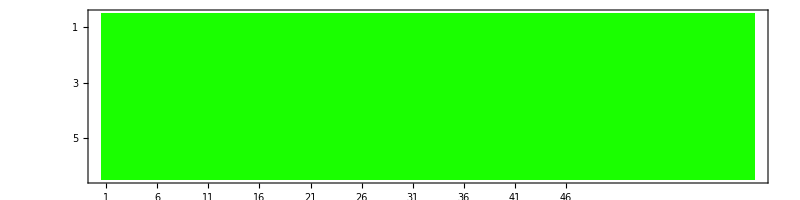

```mathematica
goodADC = Transpose[Transpose[ADCSim0[numBits]]⟦2⟧];
pgood=MatrixPlot[goodADC,Mesh-> False,ColorFunction->grnBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}]
```

Evaluate how a mismatched ADC would operate

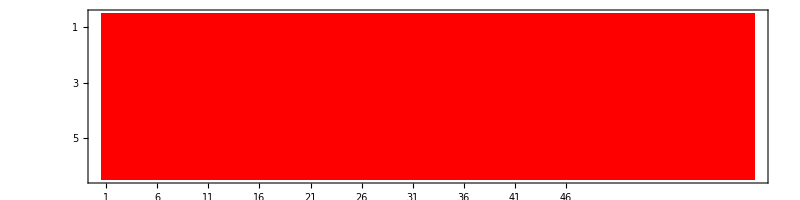

```mathematica
adcOutputs =ADCSim[0,#,numBits,seedNumber]&/@σns;
badADC=Transpose[Transpose[adcOutputs⟦1⟧]⟦2⟧];
p1 = MatrixPlot[badADC,Mesh->False,ColorFunction->redBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}]
```

Because, in some cases, I am picking more than one sample per decoded value, I wanted to create a backdrop to easily guide the eyes in a later plot to show what the actual bit resolution is for the various decode-able values.  This background plot is what pBR represents.

Show overlapping plots of how well the mismatched ADC lines up with a perfect ADC.  Any bright green spots means that the mismatched ADC didn’t code a bit that the perfect ADC says it should have.  Alternatively, any pink spot indicates the mismatched ADC coded for an extra bit that wasn’t supposed to be coded for.

```mathematica
bitResolution=Table[Table[Mod[Ceiling[i/2],2],{i,2^(numBits+1)}],{numBits}];
bitResolution=Table[Table[Mod[i,2],{i,2^numBits}],{numBits}];
pBR= MatrixPlot[bitResolution,Mesh->False,ColorFunction->gryBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}];
Show[pBR,pgood,p1]
```

-Graphics-

#### Determine correct number of decode messages

```mathematica
{goodADC,badADC};
bitDiff=Abs[Differences[{goodADC,badADC}]]⟦1⟧
errantInputs=Fold[BitOr,bitDiff⟦1⟧,bitDiff⟦2;;⟧]
totErrInputs=Total[errantInputs];
Length[errantInputs];
Grid[{{Text["Number of Errant Inputs:"],totErrInputs},
{Text["Number of Inputs:"],Length[errantInputs]},
{Text["Percent Errors:"],totErrInputs/Length[errantInputs]//N}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

{0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

Number of Errant Inputs: | 52
Number of Inputs: | 64
Percent Errors: | 0.8125

#### View actual “current” values at each stage of the ADC

In case I want to see what values were decoded for this single ADC, I would use this line to trace out the code

```mathematica
adcOutputs
```

(({1/32,31/32,0} | {0.0417205,0.935569,0} | {0.079861,0.893607,0}
0 | 0 | 0) | ({3/32,29/32,0} | {0.125162,0.806706,0} | {0.239583,0.68082,0}
0 | 0 | 0) | ({5/32,27/32,0} | {0.208603,0.677843,0} | {0.399305,0.468033,0}
0 | 0 | 0) | ({7/32,25/32,0} | {0.292044,0.54898,0} | {0.559027,0.255246,1}
0 | 0 | 1) | ({9/32,23/32,0} | {0.375485,0.420117,0} | {0.694394,0.103367,1}
0 | 0 | 1) | ({11/32,21/32,0} | {0.458926,0.291254,1} | {0.483836,0.248136,1}
0 | 1 | 1) | ({13/32,19/32,0} | {0.542367,0.162391,1} | {0.269767,0.435364,0}
0 | 1 | 0) | ({15/32,17/32,0} | {0.625808,0.0335279,1} | {0.0556972,0.622593,0}
0 | 1 | 0) | ({17/32,15/32,1} | {0.709249,0.,1} | {0,0.735306,0}
1 | 1 | 0) | ({19/32,13/32,1} | {0.771089,0.122936,1} | {0.204223,0.703328,0}
1 | 1 | 0) | ({21/32,11/32,1} | {0.65246,0.262304,1} | {0.435745,0.471407,0}
1 | 1 | 0) | ({23/32,9/32,1} | {0.533831,0.401673,1} | {0.667266,0.239487,1}
1 | 1 | 1) | ({25/32,7/32,1} | {0.415202,0.541041,0} | {0.794774,0.131003,1}
1 | 0 | 1) | ({27/32,5/32,1} | {0.296573,0.68041,0} | {0.567696,0.382121,1}
1 | 0 | 1) | ({29/32,3/32,1} | {0.177944,0.819778,0} | {0.340618,0.640805,0}
1 | 0 | 0) | ({31/32,1/32,1} | {0.0593145,0.959147,0} | {0.113539,0.899489,0}
1 | 0 | 0))

### Theoretical and numerical analysis of B ADC stages assuming 1 given ADC with continuous inputs

This analysis does the same thing as the previous analysis, but with the goal of finding the tipping points at which the ADC will switch from one output code to another.

This following code sweeps over all 2^numB possible inputs, where numB is the number of bit resolution of the ADC (in other words, numB is the number of stages that the signal 
gets passed through).  Unlike the previous section which swept over this range using a discrete number of samples, this code will try to sweep over this region in a continuous 
manner, so that we can solve for exactly where output codes will switch from one stage to another.

#### Function to simulate an ideal/perfect ADC (one with no mismatch)

ADCSim0 is the function that calculates how an ideal ADC would perform for numB0 worth of stages

```mathematica
ADCSim0[numB0_]:=
Module[{numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
ISoutVal = ISout[ISin,IRin,1,1,1,1,1,1,1,1];
IRoutVal = IRout[ISin,IRin,1,1,1,1,1,1];
{ISoutVal,IRoutVal,Dout[Rationalize[ISoutVal],Rationalize[IRoutVal]]}
];
SweepISin[inputNum_]:=
Module[{num=inputNum},
ISin0=(2num-1)/2^(numB+1);
IRin0=1-ISin0;
out = NestList[distIout, {ISin0,IRin0, Dout[ISin0,IRin0]},numB-1];
List[
out,
Transpose[out]⟦3⟧
]
];
SweepISin[#]&/@Table[i,{i,2^numB}]
]
```

#### Function to simulate a mismatched ADC

ADCSim is a function that calculates how an ADC would operate if it had to output numB0 worth of stages

```mathematica
ADCSim[μn0_,σn0_,numB0_, seedNum_]:=
Module[{μn=μn0, σn=σn0, numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
ISoutVal = ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4];
rR1=RandomVariate[LNDist];
sS4=RandomVariate[LNDist];
IRoutVal = IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4];
{ISoutVal,IRoutVal,Dout[ISoutVal,IRoutVal]}
];
SweepISin[inputNum_]:=
Module[{num=inputNum},
SeedRandom[seedNum];
ISin0=(2num-1)/2^(numB+1);
IRin0=1-ISin0;
out = NestList[distIout, {ISin0,IRin0, Dout[ISin0,IRin0]},numB-1];
List[
out,
Transpose[out]⟦3⟧
]
];
SweepISin[#]&/@Table[i,{i,2^numB}]
]
```

```mathematica
ADCSim2[μn0_,σn0_,numB0_, seedNum_]:=
Module[{μn=μn0, σn=σn0, numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
ISoutVal = ISoutList[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4];
rR1=RandomVariate[LNDist];
sS4=RandomVariate[LNDist];
IRoutVal = IRoutList[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4];
{ISoutVal,IRoutVal,Dout[ISoutVal,IRoutVal]}
];
SweepIout[ISins_,IRins_]:=
Module[{ISs=ISins,IRs=IRins},
SeedRandom[seedNum];
out = NestList[distIout, {ISs,IRs, Dout[ISs,IRs]},numB-1];
List[
out(*,
Transpose[out]⟦3⟧*)
]
];
ISins=(2*Range[1,2^numB,1]-1)/2^(numB+1);
IRins=1-ISins;
SweepIout[ISins,IRins]
]
```

```mathematica
a =ADCSim[0, 0.125, 4, 1234]
a2 =ADCSim2[0, 0.125, 4, 1234]
```

((1/32 | 31/32 | 0
0.0417205 | 0.946767 | 0
0.0924541 | 0.902393 | 0
0.25008 | 0.776879 | 0) | {0,0,0,0}
(3/32 | 29/32 | 0
0.125162 | 0.840302 | 0
0.277362 | 0.707179 | 0
0.75024 | 0.330636 | 1) | {0,0,0,1}
(5/32 | 27/32 | 0
0.208603 | 0.733837 | 0
0.462271 | 0.511965 | 0
0.970945 | 0.0266785 | 1) | {0,0,0,1}
(7/32 | 25/32 | 0
0.292044 | 0.627372 | 0
0.647179 | 0.316751 | 1
0.600721 | 0.42021 | 1) | {0,0,1,1}
(9/32 | 23/32 | 0
0.375485 | 0.520907 | 0
0.832087 | 0.121537 | 1
0.230496 | 0.813742 | 0) | {0,0,1,0}
(11/32 | 21/32 | 0
0.458926 | 0.414442 | 1
0.907562 | 0. | 1
0. | 1.01443 | 0) | {0,1,1,0}
(13/32 | 19/32 | 0
0.542367 | 0.307977 | 1
0.689328 | 0.151446 | 1
0.287218 | 0.625545 | 0) | {0,1,1,0}
(15/32 | 17/32 | 0
0.625808 | 0.201512 | 1
0.451033 | 0.352086 | 1
0.667734 | 0.167145 | 1) | {0,1,1,1}
(17/32 | 15/32 | 1
0.709249 | 0.105837 | 1
0.23689 | 0.540288 | 0
0.640766 | 0.21869 | 1) | {1,1,0,1}
(19/32 | 13/32 | 1
0.771089 | 0.125766 | 1
0.281496 | 0.57506 | 0
0.761422 | 0.192906 | 1) | {1,1,0,1}
(21/32 | 11/32 | 1
0.65246 | 0.240742 | 1
0.53884 | 0.331752 | 1
0.629169 | 0.284756 | 1) | {1,1,1,1}
(23/32 | 9/32 | 1
0.533831 | 0.355718 | 1
0.796184 | 0.0884431 | 1
0.167733 | 0.805287 | 0) | {1,1,1,0}
(25/32 | 7/32 | 1
0.415202 | 0.470694 | 0
0.920101 | 0.0290805 | 1
0.0551513 | 1.00062 | 0) | {1,0,1,0}
(27/32 | 5/32 | 1
0.296573 | 0.585669 | 0
0.657215 | 0.270231 | 1
0.512496 | 0.475955 | 1) | {1,0,1,1}
(29/32 | 3/32 | 1
0.177944 | 0.700645 | 0
0.394329 | 0.511382 | 0
0.96984 | 0. | 1) | {1,0,0,1}
(31/32 | 1/32 | 1
0.0593145 | 0.815621 | 0
0.131443 | 0.752533 | 0
0.355542 | 0.574088 | 0) | {1,0,0,0})

((1/32 | 3/32 | 5/32 | 7/32 | 9/32 | 11/32 | 13/32 | 15/32 | 17/32 | 19/32 | 21/32 | 23/32 | 25/32 | 27/32 | 29/32 | 31/32
31/32 | 29/32 | 27/32 | 25/32 | 23/32 | 21/32 | 19/32 | 17/32 | 15/32 | 13/32 | 11/32 | 9/32 | 7/32 | 5/32 | 3/32 | 1/32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1) | (0.0417205 | 0.125162 | 0.208603 | 0.292044 | 0.375485 | 0.458926 | 0.542367 | 0.625808 | 0.709249 | 0.771089 | 0.65246 | 0.533831 | 0.415202 | 0.296573 | 0.177944 | 0.0593145
0.946767 | 0.840302 | 0.733837 | 0.627372 | 0.520907 | 0.414442 | 0.307977 | 0.201512 | 0.105837 | 0.125766 | 0.240742 | 0.355718 | 0.470694 | 0.585669 | 0.700645 | 0.815621
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0) | (0.0924541 | 0.277362 | 0.462271 | 0.647179 | 0.832087 | 0.907562 | 0.689328 | 0.451033 | 0.23689 | 0.281496 | 0.53884 | 0.796184 | 0.920101 | 0.657215 | 0.394329 | 0.131443
0.902393 | 0.707179 | 0.511965 | 0.316751 | 0.121537 | 0. | 0.151446 | 0.352086 | 0.540288 | 0.57506 | 0.331752 | 0.0884431 | 0.0290805 | 0.270231 | 0.511382 | 0.752533
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0) | (0.25008 | 0.75024 | 0.970945 | 0.600721 | 0.230496 | 0. | 0.287218 | 0.667734 | 0.640766 | 0.761422 | 0.629169 | 0.167733 | 0.0551513 | 0.512496 | 0.96984 | 0.355542
0.776879 | 0.330636 | 0.0266785 | 0.42021 | 0.813742 | 1.01443 | 0.625545 | 0.167145 | 0.21869 | 0.192906 | 0.284756 | 0.805287 | 1.00062 | 0.475955 | 0. | 0.574088
0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0))

```mathematica
Transpose[Transpose[a]⟦2⟧]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0)

```mathematica
Transpose[a2⟦1⟧]⟦3⟧
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0)

```mathematica
Module[{},
With[{numB=4},
ISins=(2*Range[1,2^numB,1]-1)/2^(numB+1);
IRins=1-ISins;
List[
ISins,
IRins,
Boole[Positive[ISins-IRins]],
ISoutList[ISins,IRins,1,1,1,1,1,1,1,1],
IRoutList[ISins,IRins,1,1,1,1,1,1]
]
]
]
```

(1/32 | 3/32 | 5/32 | 7/32 | 9/32 | 11/32 | 13/32 | 15/32 | 17/32 | 19/32 | 21/32 | 23/32 | 25/32 | 27/32 | 29/32 | 31/32
31/32 | 29/32 | 27/32 | 25/32 | 23/32 | 21/32 | 19/32 | 17/32 | 15/32 | 13/32 | 11/32 | 9/32 | 7/32 | 5/32 | 3/32 | 1/32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1/16 | 3/16 | 5/16 | 7/16 | 9/16 | 11/16 | 13/16 | 15/16 | 15/16 | 13/16 | 11/16 | 9/16 | 7/16 | 5/16 | 3/16 | 1/16
15/16 | 13/16 | 11/16 | 9/16 | 7/16 | 5/16 | 3/16 | 1/16 | 1/16 | 3/16 | 5/16 | 7/16 | 9/16 | 11/16 | 13/16 | 15/16)

```mathematica
TippingPoint0[μn0_,σn0_]:=
Module[{μn=μn0, σn=σn0},
sB1=1;
sB2=1;
sS1=1;
rR2=1;
sS2=1;
rR3=1;
sS3=1;
rR4=1;
rR1=1;
sS4=1;

NSolve[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4]== IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{ISin,IRin}]
]
```

```mathematica
TippingPoint[μn0_,σn0_]:=
Module[{μn=μn0, σn=σn0},
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
rR1=RandomVariate[LNDist];
sS4=RandomVariate[LNDist];

NSolve[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4]== IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{ISin,IRin}]
]
```

#### Create colors to be used for the plots

```mathematica
redBlend=(Blend[{RGBColor[1,0,0,0],RGBColor[1,0,0,0.3]},#]&);
grnBlend=(Blend[{RGBColor[0.1,1,0,0],RGBColor[0.1,1,0,0.95]},#]&);
gryBlend=(Blend[{RGBColor[0.75,0.75,0.75,0],RGBColor[0.75,0.75,0.75,0.3]},#]&);
```

#### Plot showing the decoded values for a sweep of values

For now the code sweeps one value in the middle of each decode-able region.  It does this for the sake of time.  If I want to decode more possible inputs per decode-able region, I need to make the denominator of ISin0 equal to 2^(numB+2) instead of 2^(numB+1), like it is at a bare minimum.

```mathematica
numBits = 6;
σns={0.125};
seedNumber=1234;
imgSize=800;
initInputLabel=1;
stepSize=1;
aspectR=0.25;
```

Evaluate how a perfect ADC would operate

```mathematica
goodADC = Transpose[Transpose[ADCSim0[numBits]]⟦2⟧];
pgood=MatrixPlot[goodADC,Mesh-> False,ColorFunction->grnBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}]
```

-Graphics-

Evaluate how a mismatched ADC would operate

```mathematica
adcOutputs =ADCSim[0,#,numBits,seedNumber]&/@σns;
badADC=Transpose[Transpose[adcOutputs⟦1⟧]⟦2⟧];
p1 = MatrixPlot[badADC,Mesh->False,ColorFunction->redBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}]
```

-Graphics-

Because, in some cases, I am picking more than one sample per decoded value, I wanted to create a backdrop to easily guide the eyes in a later plot to show what the actual bit resolution is for the various decode-able values.  This background plot is what pBR represents.

Show overlapping plots of how well the mismatched ADC lines up with a perfect ADC.  Any bright green spots means that the mismatched ADC didn’t code a bit that the perfect ADC says it should have.  Alternatively, any pink spot indicates the mismatched ADC coded for an extra bit that wasn’t supposed to be coded for.

```mathematica
bitResolution=Table[Table[Mod[Ceiling[i/2],2],{i,2^(numBits+1)}],{numBits}];
bitResolution=Table[Table[Mod[i,2],{i,2^numBits}],{numBits}];
pBR= MatrixPlot[bitResolution,Mesh->False,ColorFunction->gryBlend,ColorFunctionScaling->False,ImageSize->imgSize,AspectRatio->aspectR,FrameTicks->{Range[numBits],Range[initInputLabel,2^numBits,stepSize]}];
Show[pBR,pgood,p1]
```

-Graphics-

#### Determine correct number of decode messages

```mathematica
{goodADC,badADC};
bitDiff=Abs[Differences[{goodADC,badADC}]]⟦1⟧
errantInputs=Fold[BitOr,bitDiff⟦1⟧,bitDiff⟦2;;⟧]
totErrInputs=Total[errantInputs];
Length[errantInputs];
Grid[{{Text["Number of Errant Inputs:"],totErrInputs},
{Text["Number of Inputs:"],Length[errantInputs]},
{Text["Percent Errors:"],totErrInputs/Length[errantInputs]//N}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

{0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

Number of Errant Inputs: | 52
Number of Inputs: | 64
Percent Errors: | 0.8125

#### View actual “current” values at each stage of the ADC

In case I want to see what values were decoded for this single ADC, I would use this line to trace out the code

```mathematica
adcOutputs
```

(({1/32,31/32,0} | {0.0417205,0.935569,0} | {0.079861,0.893607,0}
0 | 0 | 0) | ({3/32,29/32,0} | {0.125162,0.806706,0} | {0.239583,0.68082,0}
0 | 0 | 0) | ({5/32,27/32,0} | {0.208603,0.677843,0} | {0.399305,0.468033,0}
0 | 0 | 0) | ({7/32,25/32,0} | {0.292044,0.54898,0} | {0.559027,0.255246,1}
0 | 0 | 1) | ({9/32,23/32,0} | {0.375485,0.420117,0} | {0.694394,0.103367,1}
0 | 0 | 1) | ({11/32,21/32,0} | {0.458926,0.291254,1} | {0.483836,0.248136,1}
0 | 1 | 1) | ({13/32,19/32,0} | {0.542367,0.162391,1} | {0.269767,0.435364,0}
0 | 1 | 0) | ({15/32,17/32,0} | {0.625808,0.0335279,1} | {0.0556972,0.622593,0}
0 | 1 | 0) | ({17/32,15/32,1} | {0.709249,0.,1} | {0,0.735306,0}
1 | 1 | 0) | ({19/32,13/32,1} | {0.771089,0.122936,1} | {0.204223,0.703328,0}
1 | 1 | 0) | ({21/32,11/32,1} | {0.65246,0.262304,1} | {0.435745,0.471407,0}
1 | 1 | 0) | ({23/32,9/32,1} | {0.533831,0.401673,1} | {0.667266,0.239487,1}
1 | 1 | 1) | ({25/32,7/32,1} | {0.415202,0.541041,0} | {0.794774,0.131003,1}
1 | 0 | 1) | ({27/32,5/32,1} | {0.296573,0.68041,0} | {0.567696,0.382121,1}
1 | 0 | 1) | ({29/32,3/32,1} | {0.177944,0.819778,0} | {0.340618,0.640805,0}
1 | 0 | 0) | ({31/32,1/32,1} | {0.0593145,0.959147,0} | {0.113539,0.899489,0}
1 | 0 | 0))

### Appendix

```mathematica
GoodADCSimOutput = ADCSim[0,0.00000001,4,1234]
GoodADCGrayCodeOutput = Transpose[GoodADCSimOutput]⟦2⟧
```

(({1/32,31/32,0} | {0.0625,0.9375,0} | {0.125,0.875,0} | {0.25,0.75,0}) | (0 | 0 | 0 | 0)
({3/32,29/32,0} | {0.1875,0.8125,0} | {0.375,0.625,0} | {0.75,0.25,1}) | (0 | 0 | 0 | 1)
({5/32,27/32,0} | {0.3125,0.6875,0} | {0.625,0.375,1} | {0.75,0.25,1}) | (0 | 0 | 1 | 1)
({7/32,25/32,0} | {0.4375,0.5625,0} | {0.875,0.125,1} | {0.25,0.75,0}) | (0 | 0 | 1 | 0)
({9/32,23/32,0} | {0.5625,0.4375,1} | {0.875,0.125,1} | {0.25,0.75,0}) | (0 | 1 | 1 | 0)
({11/32,21/32,0} | {0.6875,0.3125,1} | {0.625,0.375,1} | {0.75,0.25,1}) | (0 | 1 | 1 | 1)
({13/32,19/32,0} | {0.8125,0.1875,1} | {0.375,0.625,0} | {0.75,0.25,1}) | (0 | 1 | 0 | 1)
({15/32,17/32,0} | {0.9375,0.0625,1} | {0.125,0.875,0} | {0.25,0.75,0}) | (0 | 1 | 0 | 0)
({17/32,15/32,1} | {0.9375,0.0625,1} | {0.125,0.875,0} | {0.25,0.75,0}) | (1 | 1 | 0 | 0)
({19/32,13/32,1} | {0.8125,0.1875,1} | {0.375,0.625,0} | {0.75,0.25,1}) | (1 | 1 | 0 | 1)
({21/32,11/32,1} | {0.6875,0.3125,1} | {0.625,0.375,1} | {0.75,0.25,1}) | (1 | 1 | 1 | 1)
({23/32,9/32,1} | {0.5625,0.4375,1} | {0.875,0.125,1} | {0.25,0.75,0}) | (1 | 1 | 1 | 0)
({25/32,7/32,1} | {0.4375,0.5625,0} | {0.875,0.125,1} | {0.25,0.75,0}) | (1 | 0 | 1 | 0)
({27/32,5/32,1} | {0.3125,0.6875,0} | {0.625,0.375,1} | {0.75,0.25,1}) | (1 | 0 | 1 | 1)
({29/32,3/32,1} | {0.1875,0.8125,0} | {0.375,0.625,0} | {0.75,0.25,1}) | (1 | 0 | 0 | 1)
({31/32,1/32,1} | {0.0625,0.9375,0} | {0.125,0.875,0} | {0.25,0.75,0}) | (1 | 0 | 0 | 0))

({0,0,0,0}
{0,0,0,1}
{0,0,1,1}
{0,0,1,0}
{0,1,1,0}
{0,1,1,1}
{0,1,0,1}
{0,1,0,0}
{1,1,0,0}
{1,1,0,1}
{1,1,1,1}
{1,1,1,0}
{1,0,1,0}
{1,0,1,1}
{1,0,0,1}
{1,0,0,0})

```mathematica
OkayADCSimOutput = ADCSim[0,0.0125, 4,1234]
OkayADCGrayCodeOutput = Transpose[OkayADCSimOutput]⟦2⟧
```

(({1/32,31/32,0} | {0.060017,0.937312,0} | {0.119504,0.87726,0} | {0.241709,0.757584,0}) | (0 | 0 | 0 | 0)
({3/32,29/32,0} | {0.180051,0.811936,0} | {0.358513,0.631781,0} | {0.725126,0.272753,1}) | (0 | 0 | 0 | 1)
({5/32,27/32,0} | {0.300085,0.68656,0} | {0.597522,0.386302,1} | {0.7969,0.209184,1}) | (0 | 0 | 1 | 1)
({7/32,25/32,0} | {0.420119,0.561184,0} | {0.83653,0.140823,1} | {0.290502,0.688402,0}) | (0 | 0 | 1 | 0)
({9/32,23/32,0} | {0.540153,0.435808,1} | {0.855585,0.116904,1} | {0.24116,0.730907,0}) | (0 | 1 | 1 | 0)
({11/32,21/32,0} | {0.660187,0.310432,1} | {0.609445,0.359696,1} | {0.742016,0.24729,1}) | (0 | 1 | 1 | 1)
({13/32,19/32,0} | {0.780221,0.185056,1} | {0.363305,0.602489,0} | {0.734818,0.238662,1}) | (0 | 1 | 0 | 1)
({15/32,17/32,0} | {0.900255,0.0596804,1} | {0.117165,0.845281,0} | {0.236978,0.727948,0}) | (0 | 1 | 0 | 0)
({17/32,15/32,1} | {0.932399,0.0553451,1} | {0.108654,0.881771,0} | {0.219763,0.772961,0}) | (1 | 1 | 0 | 0)
({19/32,13/32,1} | {0.808079,0.181679,1} | {0.356674,0.633743,0} | {0.721406,0.276557,1}) | (1 | 1 | 0 | 1)
({21/32,11/32,1} | {0.683759,0.308012,1} | {0.604694,0.385715,1} | {0.79569,0.21686,1}) | (1 | 1 | 1 | 1)
({23/32,9/32,1} | {0.55944,0.434346,1} | {0.852713,0.137687,1} | {0.284034,0.707514,0}) | (1 | 1 | 1 | 0)
({25/32,7/32,1} | {0.43512,0.560679,0} | {0.866399,0.125308,1} | {0.258498,0.733296,0}) | (1 | 0 | 1 | 0)
({27/32,5/32,1} | {0.3108,0.687013,0} | {0.618857,0.376034,1} | {0.775718,0.240447,1}) | (1 | 0 | 1 | 1)
({29/32,3/32,1} | {0.18648,0.813346,0} | {0.371314,0.626759,0} | {0.751017,0.254912,1}) | (1 | 0 | 0 | 1)
({31/32,1/32,1} | {0.06216,0.93968,0} | {0.123771,0.877484,0} | {0.250339,0.753535,0}) | (1 | 0 | 0 | 0))

({0,0,0,0}
{0,0,0,1}
{0,0,1,1}
{0,0,1,0}
{0,1,1,0}
{0,1,1,1}
{0,1,0,1}
{0,1,0,0}
{1,1,0,0}
{1,1,0,1}
{1,1,1,1}
{1,1,1,0}
{1,0,1,0}
{1,0,1,1}
{1,0,0,1}
{1,0,0,0})

```mathematica
BadADCSimOutput = ADCSim[0,0.125, 4,1234]
BadADCGrayCodeOutput = Transpose[BadADCSimOutput]⟦2⟧
```

(({1/32,31/32,0} | {0.0417205,0.935569,0} | {0.079861,0.893607,0} | {0.178757,0.812592,0}) | (0 | 0 | 0 | 0)
({3/32,29/32,0} | {0.125162,0.806706,0} | {0.239583,0.68082,0} | {0.536272,0.437775,1}) | (0 | 0 | 0 | 1)
({5/32,27/32,0} | {0.208603,0.677843,0} | {0.399305,0.468033,0} | {0.893787,0.0629589,1}) | (0 | 0 | 0 | 1)
({7/32,25/32,0} | {0.292044,0.54898,0} | {0.559027,0.255246,1} | {0.699666,0.274279,1}) | (0 | 0 | 1 | 1)
({9/32,23/32,0} | {0.375485,0.420117,0} | {0.694394,0.103367,1} | {0.283343,0.531737,0}) | (0 | 0 | 1 | 0)
({11/32,21/32,0} | {0.458926,0.291254,1} | {0.483836,0.248136,1} | {0.680175,0.213052,1}) | (0 | 1 | 1 | 1)
({13/32,19/32,0} | {0.542367,0.162391,1} | {0.269767,0.435364,0} | {0.603834,0.1617,1}) | (0 | 1 | 0 | 1)
({15/32,17/32,0} | {0.625808,0.0335279,1} | {0.0556972,0.622593,0} | {0.12467,0.566091,0}) | (0 | 1 | 0 | 0)
({17/32,15/32,1} | {0.709249,0.,1} | {0.,0.735306,0} | {0.,0.735306,0}) | (1 | 1 | 0 | 0)
({19/32,13/32,1} | {0.771089,0.122936,1} | {0.204223,0.703328,0} | {0.457125,0.496154,0}) | (1 | 1 | 0 | 0)
({21/32,11/32,1} | {0.65246,0.262304,1} | {0.435745,0.471407,0} | {0.975353,0.0293667,1}) | (1 | 1 | 0 | 1)
({23/32,9/32,1} | {0.533831,0.401673,1} | {0.667266,0.239487,1} | {0.656467,0.385658,1}) | (1 | 1 | 1 | 1)
({25/32,7/32,1} | {0.415202,0.541041,0} | {0.794774,0.131003,1} | {0.359099,0.597254,0}) | (1 | 0 | 1 | 0)
({27/32,5/32,1} | {0.296573,0.68041,0} | {0.567696,0.382121,1} | {1.04745,0.168642,1}) | (1 | 0 | 1 | 1)
({29/32,3/32,1} | {0.177944,0.819778,0} | {0.340618,0.640805,0} | {0.762424,0.295266,1}) | (1 | 0 | 0 | 1)
({31/32,1/32,1} | {0.0593145,0.959147,0} | {0.113539,0.899489,0} | {0.254141,0.78431,0}) | (1 | 0 | 0 | 0))

({0,0,0,0}
{0,0,0,1}
{0,0,0,1}
{0,0,1,1}
{0,0,1,0}
{0,1,1,1}
{0,1,0,1}
{0,1,0,0}
{1,1,0,0}
{1,1,0,0}
{1,1,0,1}
{1,1,1,1}
{1,0,1,0}
{1,0,1,1}
{1,0,0,1}
{1,0,0,0})

```mathematica
Grid[{{GoodADCGrayCodeOutput,BitXor[GoodADCGrayCodeOutput,OkayADCGrayCodeOutput],BitXor[GoodADCGrayCodeOutput,BadADCGrayCodeOutput]}}]
```

({0,0,0,0}
{0,0,0,1}
{0,0,1,1}
{0,0,1,0}
{0,1,1,0}
{0,1,1,1}
{0,1,0,1}
{0,1,0,0}
{1,1,0,0}
{1,1,0,1}
{1,1,1,1}
{1,1,1,0}
{1,0,1,0}
{1,0,1,1}
{1,0,0,1}
{1,0,0,0}) | ({0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}) | ({0,0,0,0}
{0,0,0,0}
{0,0,1,0}
{0,0,0,1}
{0,1,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,1}
{0,0,1,0}
{0,0,0,1}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0}
{0,0,0,0})

#### Optimizing recursive loops by trying to eliminate the Transformed Distribution calculation

Timing comparisons to try and optimize recursive loop

```mathematica
With[{μn=0,σn=0.125,ISin=1/32,IRin=31/32},
SeedRandom[1234];
distISout = TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
List[sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4,RandomVariate[distISout]]
]//Timing
```

{0.00913,{0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.0417205}}

```mathematica
With[{μn=0,σn=0.125,ISin=1/32,IRin=31/32},
SeedRandom[1234];
LNDist = LogNormalDistribution[μn,σn];
ISoutVal = ISout[ISin,IRin,sB1=RandomVariate[LNDist],sB2=RandomVariate[LNDist],
sS1=RandomVariate[LNDist],rR2=RandomVariate[LNDist],sS2=RandomVariate[LNDist],
rR3=RandomVariate[LNDist],sS3=RandomVariate[LNDist],rR4=RandomVariate[LNDist]];
List[sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4,ISoutVal]
]//Timing
```

{0.00155,{0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.0417205}}

```mathematica
With[{μn=0,σn=0.125,ISin=1/32,IRin=31/32},
SeedRandom[1234];
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
ISoutVal = ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4];
List[sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4,ISoutVal]
]//Timing
```

{0.00135,{0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.0417205}}

The following code tests and shows that any given stage of the ADC will always use the same mismatch parameters regardless of what the Signal Input is equal to.  It also shows that each stage has different mismatch parameters compared to the other stages.

```mathematica
ADCSimTest[μn0_,σn0_,numB0_, seedNum_]:=
Module[{μn=μn0, σn=σn0, numB=numB0},
distIout[inputs_]:=
Module[{ISin=inputs⟦1⟧, IRin=inputs⟦2⟧},
LNDist = LogNormalDistribution[μn,σn];
sB1=RandomVariate[LNDist];
sB2=RandomVariate[LNDist];
sS1=RandomVariate[LNDist];
rR2=RandomVariate[LNDist];
sS2=RandomVariate[LNDist];
rR3=RandomVariate[LNDist];
sS3=RandomVariate[LNDist];
rR4=RandomVariate[LNDist];
ISoutVal = ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4];
rR1=RandomVariate[LNDist];
sS4=RandomVariate[LNDist];
IRoutVal = IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4];
{ISoutVal,IRoutVal,Dout[ISoutVal,IRoutVal],sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4,rR1,sS4}
];
SweepISin[inputNum_]:=
Module[{num=inputNum},
SeedRandom[seedNum];
ISin0=(2num-1)/2^(numB+1);
IRin0=1-ISin0;
out = NestList[distIout, {ISin0,IRin0, Dout[ISin0,IRin0]},numB-1];
List[
out(*,
Transpose[out]⟦3⟧*)
]
];
SweepISin[#]&/@Table[i,{i,2^numB}]
]
ADCSimTest[0,0.125,3,1234]
```

({{1/16,15/16,0},{0.0834411,0.893535,0,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.184908,0.804786,0,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{3/16,13/16,0},{0.250323,0.680605,0,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.554725,0.414358,1,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{5/16,11/16,0},{0.417205,0.467674,0,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.924541,0.0239301,1,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{7/16,9/16,0},{0.584088,0.254744,1,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.57018,0.251766,1,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{9/16,7/16,1},{0.75097,0.110093,1,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.246414,0.574341,0,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{11/16,5/16,1},{0.593145,0.29823,1,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.667512,0.210097,1,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{13/16,3/16,1},{0.355887,0.528182,0,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.788658,0.149656,1,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}}
{{15/16,1/16,1},{0.118629,0.758133,0,0.938435,0.819356,1.39759,0.872127,1.01311,1.00448,1.12393,0.988694,0.955576,0.983126},{0.262886,0.631958,0,1.07224,1.00125,0.892745,1.06313,0.945119,1.01857,1.17351,0.930058,1.07209,0.949533}})